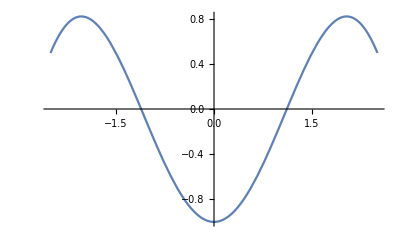

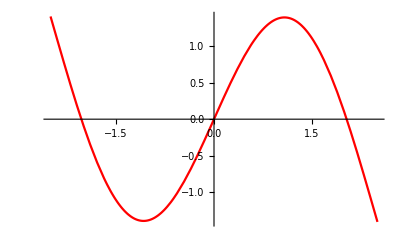

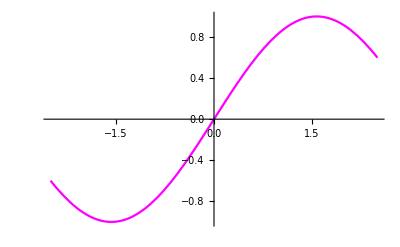

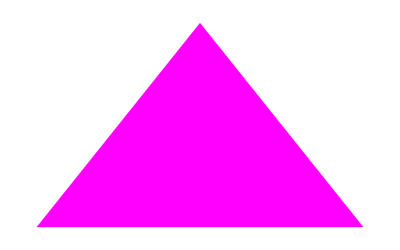

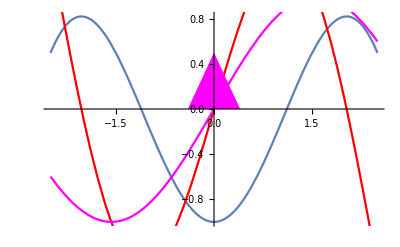

```mathematica
p1=Plot[x Sin[x]-1,{x,-2.5,2.5}]
p2=Plot[Evaluate[D[x Sin[x]-1,x]],{x,-2.5,2.5}, PlotStyle->Red]
p3=Plot[Sin[x],{x,-2.5,2.5},PlotStyle->Magenta]
p4 = Graphics[{Magenta,Polygon[{{0.4,0},{0,0.5},{-0.4,0}}]}]

Show[p1,p2,p3,p4]
```

```mathematica
p2=Plot[Evaluate[D[x Sin[x]-1,x]],{x,-2.5,2.5}PlotStyle->Red]
```

Plot::pllim: Range specification {x,-2.5,2.5} PlotStyle→Red is not of the form {x, xmin, xmax}.

```mathematica
Plot[x Cos[x]+Sin[x],{x,-2.5,2.5}, PlotStyle->Red]
```

-Graphics-

```mathematica
poisson[r_, theta_]:= (1 - r^2)/(1 + r^2 - 2 *r *Cos(theta))
```

```mathematica
a = poisson[0,Pi]
```

```mathematica
p1=Plot[x Sin[x]-1,{x,-2.5,2.5}]
p2=Plot[Evaluate[D[x Sin[x]-1,x]],{x,-2.5,2.5}, PlotStyle->Red]
p3=Plot[Sin[x],{x,-2.5,2.5},PlotStyle->Magenta]
p4 = Graphics[{Magenta,Polygon[{{0.4,0},{0,0.5},{-0.4,0}}]}]

Show[p1,p2,p3,p4]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

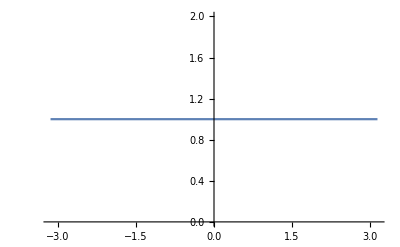

-Graphics-

-Graphics-

-Graphics-

```mathematica
p0=Plot[poisson[0, theta],{theta,- Pi, Pi}]
p13=Plot[poisson[1/3, theta],{theta,- Pi, Pi}, PlotStyle->Red]
p23 = Plot[poisson[2/3, theta],{theta,- Pi, Pi}, PlotStyle->Gray]

Show[p0,p13,p23]
```

```mathematica
poisson[1/3, 0]
```

4/5

```mathematica
r0=Plot[poisson[0, theta],{theta,- Pi, Pi}]
r13=Plot[poisson[1/3, theta],{theta,- Pi, Pi}, PlotStyle->Red]
r23 = Plot[poisson[2/3, theta],{theta,- Pi, Pi}, PlotStyle->Gray]

Show[r0,r13,r23]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
r0=Plot[poisson[0, theta],{theta,- Pi, Pi}]
r13=Plot[poisson[1/3, theta],{theta,- Pi, Pi}, PlotStyle->Red]
r23 = Plot[poisson[2/3, theta],{theta,- Pi, Pi}, PlotStyle->Gray]

Show[r0,r13,r23]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
r13=Plot[poisson[1/3, theta],{theta,- Pi, Pi}, PlotStyle->Red]
```

-Graphics-

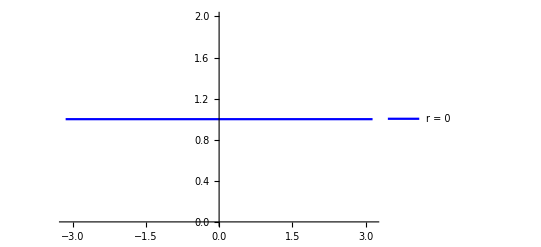

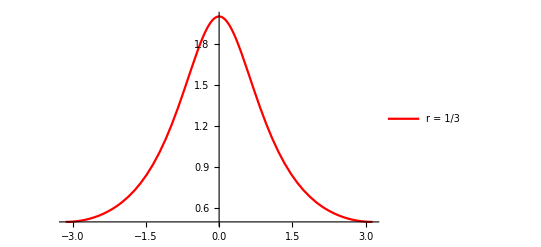

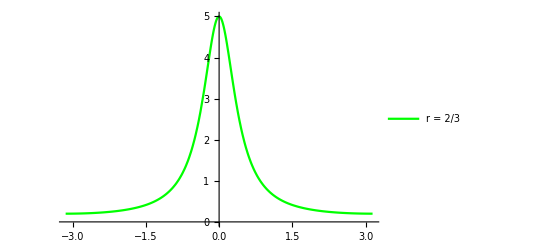

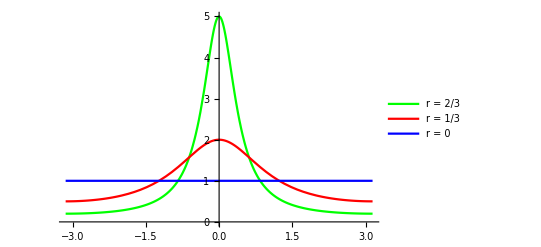

```mathematica
poisson[r_, theta_]:= (1 - r^2)/(1 + r^2 - 2 *r *Cos(theta))
r0=Plot[1,{theta,- Pi, Pi}, PlotStyle->Blue, PlotLegends -> {"r = 0"}]
r13=Plot[(1 - (1/3)^2)/(1 + (1/3)^2 - 2 *(1/3) *Cos[theta]),{theta,- Pi, Pi}, PlotStyle->Red, PlotLegends -> {"r = 1/3"}]
r23 = Plot[(1 - (2/3)^2)/(1 + (2/3)^2 - 2 *(2/3) *Cos[theta]),{theta,- Pi, Pi}, PlotStyle->Green,  PlotLegends -> {"r = 2/3"}]
Show[r23, r13, r0]
```

```mathematica
Legended[-Graphics-, Placed[
 
    LineLegend[{Directive[Opacity[1.], AbsoluteThickness[1.6], RGBColor[0, 1, 0]]}, {r = 2/3}, LegendMarkers -> None, LabelStyle -> {}, LegendLayout -> Column], After]]

    LineLegend[{Directive[Opacity[1.], AbsoluteThickness[1.6], RGBColor[1, 0, 0]]}, {r = 1/3}, LegendMarkers -> None, LabelStyle -> {}, LegendLayout -> Column]

    LineLegend[{Directive[Opacity[1.], AbsoluteThickness[1.6], RGBColor[0, 0, 1]]}, {r = 0}, LegendMarkers -> None, LabelStyle -> {}, LegendLayout -> Column]
```

```mathematica
poisson[r_, theta_]:= (1 - r^2)/(1 + r^2 - 2 *r *Cos(theta))
r0=Plot[1,{theta,- Pi, Pi}, PlotStyle->Blue, PlotLegends -> {"r = 0"}]
r13=Plot[(1 - (1/3)^2)/(1 + (1/3)^2 - 2 *(1/3) *Cos[theta]),{theta,- Pi, Pi}, PlotStyle->Red, PlotLegends -> {"r = 1/3"}]
r23 = Plot[(1 - (2/3)^2)/(1 + (2/3)^2 - 2 *(2/3) *Cos[theta]),{theta,- Pi, Pi}, PlotStyle->Green,  PlotLegends -> {"r = 2/3"}]
Show[r23, r13, r0]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
A = Show[r23, r13, r0]
```

-Graphics-

```mathematica
Export["grafi.png",A]
```

grafi.png